```mathematica
ClearAll["Global`*"]
```

### Simple Exponential Decay

```mathematica
Pup[t_, Γ_, Ω_] := 1/2+  1/2(Exp[- (t/Γ )^2])Sin[2π Ω t - π/2 ]
ExpDecay[t_, Γ_]:=  1/2(Exp[-(t/Γ)^2]) + 1/2;
```

```mathematica
dataUp  =  {0.000596086098654914,20.588394265716953,57.352993871287914,85.7141320146891,99.99940391390135,76.26056050201872,47.89915687493907,13.235208783850162,0.000596086098654914,26.890757619066775,75.2100790177362,94.11763550112326,99.99940391390135,80.46202808094847,24.789920982264107,3.78151936941892,3.78151936941892,34.24371097786265,76.26056050201872,92.01676549492016,94.11763550112326}/100;
dataUp2 = {23.73943949798126,58.40340823113558,73.10924238084712,82.5629217528669,69.95800681402915,41.59659201814135,17.437078247133115,18.487395940536743,40.54607218752814,54.20169860855469,73.10924238084712,79.4116048617839}/100;
dataUp3 = {55.25213085709835,63.65545884927653,75.2100790177362,68.90753149900159,43.69743632054157,27.941040126844374,33.193297631615856,36.34454115072453,48.94957945739058,68.90753149900159,75.2100790177362,60.504142567880024,44.74786914288609,22.689070346959195,33.193297631615856,44.74786914288609,63.65545884927653,82.5629217528669,65.75628902213731,47.89915687493907,44.74786914288609}/100;
dataTime = Table[i 4, {i,0,Length[dataUp]-1}]/10^6;
dataTime2 = Table[250 + i 4, {i,0,Length[dataUp2]-1}]/10^6;
dataTime3 = Table[500 + i 4, {i, 0, Length[dataUp3]-1}]/10^6;

data = Transpose[{Join[dataTime, dataTime2, dataTime3], Join[dataUp, dataUp2,dataUp3]}];
```

```mathematica
(*fit = FindFit[dataUp, {Pup[t, Γ, Ω, B, A, ϕ0], Γ > 0, Ω > 0}, {{Γ,1000}, {Ω, 15000}, {B,0.5},{ A,.5}, {ϕ0, -π/2}}, t]
fit2 = FindFit[dataUp2, {Pup[t, Γ, Ω, B, A, ϕ0], Γ > 0, Ω > 0}, {{Γ,2000}, {Ω, 8000}, {B,0.5},{ A,.5}, {ϕ0, -π/2}}, t]*)
fit = FindFit[data, {Pup[t, Γ, Ω],  Ω > 0}, {{Γ ,0.001}, {Ω, 32000}}, t]
```

{Γ→-0.00102003,Ω→32466.}

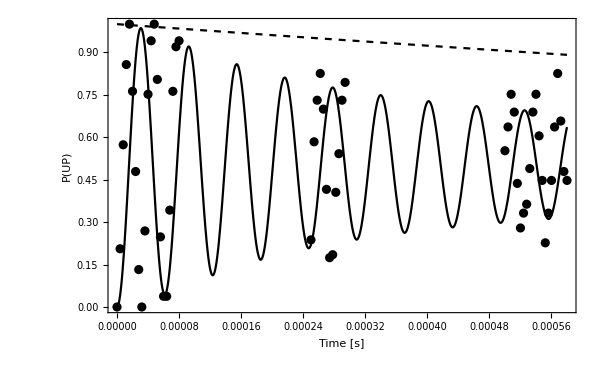

```mathematica
plot = Show[ListPlot[data , PlotStyle-> Black],
Plot[Pup[t,Γ, Ω]/.fit ,{t,0,Last[dataTime3] }, PlotStyle->Black],
Plot[ExpDecay[t,Γ]/.fit, {t,0,Last[dataTime3] }, PlotStyle-> {Black, Dashed}],

PlotRange-> {{0, Last[dataTime3]},{0,1}}, 
 Frame-> True, ImageSize-> 600, FrameLabel-> {"Time [s]","P(UP)"}, FrameStyle-> Bold, LabelStyle-> {16, Black}
]
```

```mathematica
~
```

### Rabi Spectroscopy

```mathematica
ExpDecay[t_, Γ_]:=  1/2(Exp[(- t)/Γ]) + 1/2;
QuadDecay[t_, Ω_] := (1 + ( (25.6 10^6)/Ω t)^2)^(-1/4)
QuadDecay[t_, Ω_, δz_] := (1 + ( δz/Ω t)^2)^(-1/4)
ExpDecay[t_, Γ_] := Exp[- (t/Γ)]
Pup[t_, Γ_, Ω_, δz_] := 1/2+  1/2 Sin[2π Ω t -π/2 ]  QuadDecay[t, Ω]ExpDecay[t, Γ]
```

```mathematica
fit = FindFit[data, {Pup[t, Γ, Ω, δz],  Ω > 0,0.5 ≥ Γ>0}, {{Γ ,0.01}, {Ω,32000}, {δz, 25 10^6}}, t]
```

{Γ→0.000733641,Ω→32508.3,δz→2.5×10^7}

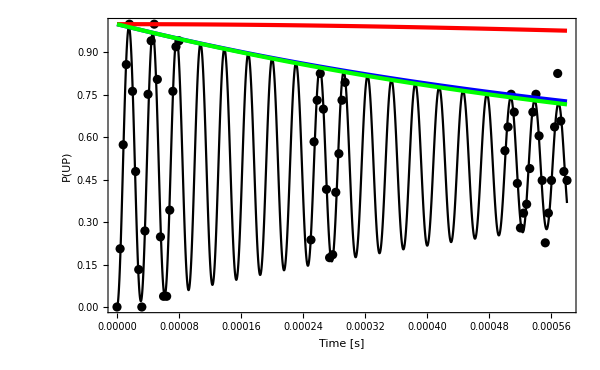

```mathematica
Show[ListPlot[data , PlotStyle-> Black],
Plot[Pup[t,Γ, Ω, δz]/.fit ,{t,0,Last[dataTime3] }, PlotStyle->Black],
Plot[ExpDecay[t,Γ]/2 + 1/2/.fit, {t,0,Last[dataTime3] }, PlotStyle-> {Blue, Thickness[0.005]}],
Plot[QuadDecay[t,Ω]/2 + 1/2/.fit, {t,0,Last[dataTime3] }, PlotStyle-> {Red, Thickness[0.005]}],
Plot[QuadDecay[t,Ω]ExpDecay[t,Γ]/2 + 1/2/.fit, {t,0,Last[dataTime3] }, PlotStyle-> {Green, Thickness[0.005]}],
PlotRange-> {{0, Last[dataTime3]},{0,1}}, 
 Frame-> True, ImageSize-> 600, FrameLabel-> {"Time [s]","P(UP)"}, FrameStyle-> Directive[{Thick,Black,  14}]]
```

```mathematica
Ωlist = {32.508, 16.176, 22.043, 43.848, 9.781};
Γlist = {0.733,5.056 , 1.385, 0.446, 1000};
```

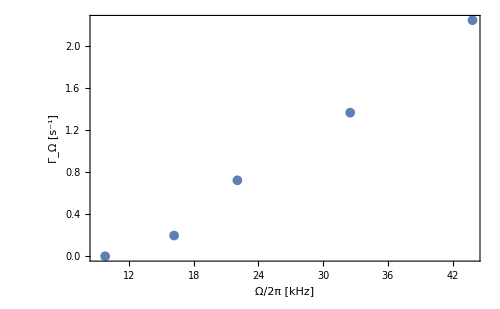

```mathematica
Show[ListPlot[Transpose[{Ωlist, 1/Γlist}], PlotMarkers->{Automatic, 10}], Frame-> True, ImageSize-> 500,  FrameLabel-> {"Ω/2π [kHz]","Γ_Ω [s^-1]"}, FrameStyle-> Directive[{Thick,Black,  14}]]
```